# Lomb–Scargle Periodogram

寻找周期性信号常用傅里叶变化，用  sinωx、cosωx  函数来作为基底，得到不同频率下的权重，来确定信号的周期；

但是在天文信号处理如脉冲周期性搜寻、双星周期确定等数据处理中，由于观测不是连续的也不是周期的、信号也不是每个都能记录到，各种缺失导致记录的数据不等距，这时就不适合用DFT、FFT等傅里叶变换方法（均匀插值也会引入失真）。

Lomb–Scargle  Periodogram (LSP) 就可以很好地用于解决这种原始不等距数据的情况，它不依赖“等间隔”这一前提。

Lomb-Scargle 周期图由 Lomb 开发，并由 Scargle 进一步扩展，用于查找和检验不规则时间采样下的弱周期信号的重要性。这里使用的算法基于加权最小二乘拟合，形式为 。

常选择C = < y (t) >，将y(t)减去均值再对每个不同的ω建立模型 ，最小二乘法的思路是希望得到一组(A,B)使得最小化残差平方和， 。

```mathematica
(*定义模型*)
model[i_]:=A Cos[ω t[i]]+B Sin[ω t[i]];

chi2 = Sum[(y[i]-model[i])^2,{i,1,n}]; (*这里chi2就代表右边的式子，也方便后面求导，但是如果使用==只是说两边组成方程关系，是个逻辑上相等的关系，常用于Solve*)

(*对 A 和 B 分别求偏导*)
eq1=D[chi2,A]==0;
eq2=D[chi2,B]==0;

Print[" = ", eq1];
Print[" = ", eq2];
```

= ∑_(i=1)^n (2 A Cos[ω t[i]]^2+2 B Cos[ω t[i]] Sin[ω t[i]]-2 Cos[ω t[i]] y[i])==0

= ∑_(i=1)^n (2 A Cos[ω t[i]] Sin[ω t[i]]+2 B Sin[ω t[i]]^2-2 Sin[ω t[i]] y[i])==0

引入时间平移因子τ，我们可以看到它能帮我们简化方程更容易得A、B 。

```mathematica
model[i_]:=A Cos[ω (t[i] - τ)]+B Sin[ω (t[i] - τ)];

chi2 = Sum[(y[i]-model[i])^2,{i,1,n}];

(*对 A 和 B 分别求偏导*)
eq1=D[chi2,A]==0;
eq2=D[chi2,B]==0;

Print[" = ", eq1];
Print[" = ", eq2];
```

= ∑_(i=1)^n (2 A Cos[ω (-τ+t[i])]^2+2 B Cos[ω (-τ+t[i])] Sin[ω (-τ+t[i])]-2 Cos[ω (-τ+t[i])] y[i])==0

= ∑_(i=1)^n (2 A Cos[ω (-τ+t[i])] Sin[ω (-τ+t[i])]+2 B Sin[ω (-τ+t[i])]^2-2 Sin[ω (-τ+t[i])] y[i])==0

如果使得，那么可以很容易解出A和B，即从中得到，即从中得到。

所以我们要在一组时间数据点{}内，对于不同频率解得不同的，然后就可以用上式简化求解 A、B。

```mathematica
Eq = Sin[2 ω t[i] - 2 ω τ] /. (2 ω  -> Ω) /. (-2 ω -> - Ω)
expandedSum=Sum[TrigExpand[Eq],{i,1,n}]
```

-Sin[τ Ω-Ω t[i]]

∑_(i=1)^n (-Cos[Ω t[i]] Sin[τ Ω]+Cos[τ Ω] Sin[Ω t[i]])

可以看出

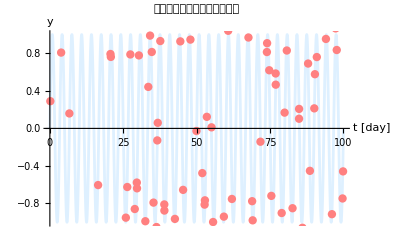

```mathematica
(* 1. 生成模拟数据 *)
SeedRandom[42];
nPoints=70;
tMax=100;
times=Sort[RandomReal[{0,tMax},nPoints]];
fTrue=0.3;                (*真实频率 day^{-1}*)
ωTrue=2 π fTrue;

signal=Sin[ωTrue times];
noise=RandomVariate[NormalDistribution[0,0.15],nPoints]; (*注入信号强度的误差*)
y=signal+noise;

(*可视化*)
Show[Plot[Sin[ωTrue t],{t,0,100},PlotStyle->LightBlue],ListPlot[Transpose[{times,y}],PlotStyle->Directive[Pink,PointSize[0.015]]],PlotLabel->"中心化后的数据与真实正弦波",AxesLabel->{"t [day]","y"}]
```

```mathematica
(* 2. 定义单个频率的 LS 功率 *)
(*Total 用于求和*)
LombScargleSingle[ω_,t_,vals_]:=Module[{n,y,S,C2,τ,cosTerm,sinTerm,num,den,totalPower},n=Length[t];
y=vals-Mean[vals];(*内部中心化，即系数C=0*)
(*正交化 τ*)
S=Total[Sin[2 ω t]];
C2=Total[Cos[2 ω t]]; (*为了与推导中的系数C区分*)
τ=If[Abs[C2]>10^-10(*防止除零*),ArcTan[S/C2]/(2 ω),0];
(*基函数*)
cosTerm=Cos[ω (t-τ)];
sinTerm=Sin[ω (t-τ)];
(*系数 A,B (对角化后)*)
num=Total[y cosTerm]^2/Total[cosTerm^2]+Total[y sinTerm]^2/Total[sinTerm^2];
totalPower=Total[y^2]/n;
(*内置默认的归一化方式*)
num/(2 totalPower)];
```

```mathematica
(* 3. 频率扫描 *)
fMin=0.01;
fMax=1.5;
nf=3000;
freqs=Subdivide[fMin,fMax,nf-1];
ωList=2 π freqs;
myLS=LombScargleSingle[#,times,y]&/@ωList;
```

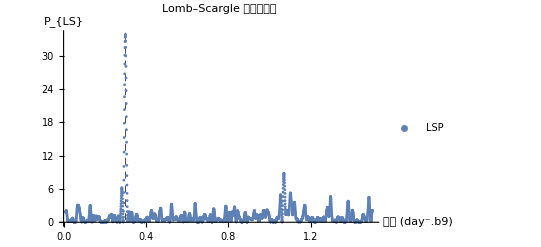

```mathematica
(* 4. 绘图对比，虚线是真实频率 *)
Show[ListPlot[Transpose[{freqs,myLS}],PlotStyle->Directive[StandardCyan,PointSize[0.005]],PlotLegends->{"LSP"}],GridLines->{{fTrue},None},GridLinesStyle->Directive[Black,Dashed](* 虚线是真实频率 *),AxesLabel->{"频率 (day⁻.b9)","P_{LS}"},PlotLabel->"Lomb–Scargle 周期图对比",PlotRange->All]
```

```mathematica
(*周期性折叠*)
(*在 freq 和 myLS 列表中找到最大功率的索引*)
maxPos=First[First[Position[myLS,Max[myLS]]]];
fBest=freqs[[maxPos]];
period=1/fBest;

Print["最佳频率：",fBest," day⁻.b9"];
Print["对应周期：",period," days"];
```

最佳频率：0.30015 day⁻.b9

对应周期：3.33167 days

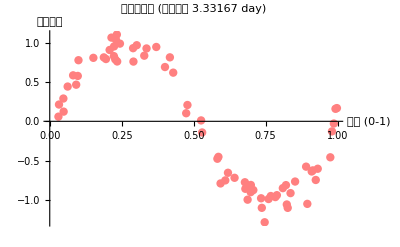

```mathematica
(*使用之前中心化后的 y*)
phase=Mod[times/period,1.0];   (*相位=(时间/周期) 的小数部分, 类似求余*)

(*散点图*)
foldPlot=ListPlot[Transpose[{phase,y}],PlotStyle->Directive[Pink,PointSize[0.015]],AxesLabel->{"相位 (0-1)","信号振幅"},PlotLabel->"相位折叠图 (最佳周期 "<>ToString[period]<>" day)"]
```

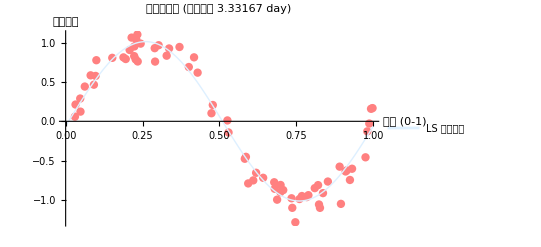

```mathematica
(*计算该频率下的振幅 A,B 和 τ*)
omegaBest=2 Pi fBest;
S=Total[Sin[2 omegaBest times]];
C2=Total[Cos[2 omegaBest times]];
tau=If[Abs[C2]>10^-10,ArcTan[S/C2]/(2 omegaBest),0];
cosTerm=Cos[omegaBest (times-tau)];
sinTerm=Sin[omegaBest (times-tau)];
A=Total[y*cosTerm]/Total[cosTerm^2];
B=Total[y*sinTerm]/Total[sinTerm^2];

(*在相位网格上计算模型值*)
phaseGrid=Subdivide[0,1,200];
modelLine=A Cos[omegaBest (phaseGrid*period-tau)]+B Sin[omegaBest (phaseGrid*period-tau)]; (* A、B 分量，没有考虑将第一个数据点的时刻作为时间零点，所以会是Sin函数存在相位偏移*)

(*添加到折叠图*)
Show[foldPlot,ListLinePlot[Transpose[{phaseGrid,modelLine}],PlotStyle->{LightBlue,Thick},PlotLegends->{"LS 拟合模型"}]]
```